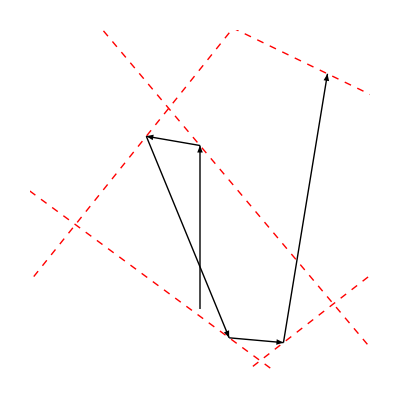

```mathematica
OutgoingArrow[incoming_Arrow,boundary_InfiniteLine,lineLength_]:=Module[{p1,p2,q1,q2,v},
{p1,p2}=Identity@@incoming;
{q1,q2}=Identity@@boundary;
v=Projection[p2-p1,q2-q1];
Arrow[{p2,p2+lineLength(p1+2v-p2)/Norm[p1+2v-p2]}]
]
SeedRandom[56];
a1=Arrow[{{0,0},{0,3}}];
b1=InfiniteLine[{{0,3},RandomReal[{-10,10},2]}];
a2=OutgoingArrow[a1,b1,1]//N;
b2=InfiniteLine[{a2[[1,2]],RandomReal[{-10,10},2]}]//N;
a3=OutgoingArrow[a2,b2,4];
b3=InfiniteLine[{a3[[1,2]],RandomReal[{-10,10},2]}]//N;
a4=OutgoingArrow[a3,b3,1];
b4=InfiniteLine[{a4[[1,2]],RandomReal[{-10,10},2]}]//N;
a5=OutgoingArrow[a4,b4,5];
b5=InfiniteLine[{a5[[1,2]],RandomReal[{-10,10},2]}]//N;
a6=OutgoingArrow[a5,b5,9];
b6=InfiniteLine[{a6[[1,2]],RandomReal[{-10,10},2]}]//N;
Graphics[{
a1,
a2,
a3,
a4,
a5,
Dashed,Red,
b1,
b2,
b3,
b4,
b5,
Nothing
},PlotRange->{{-3,3},{-1,5}},AspectRatio->1]
```